## Immunity gaps

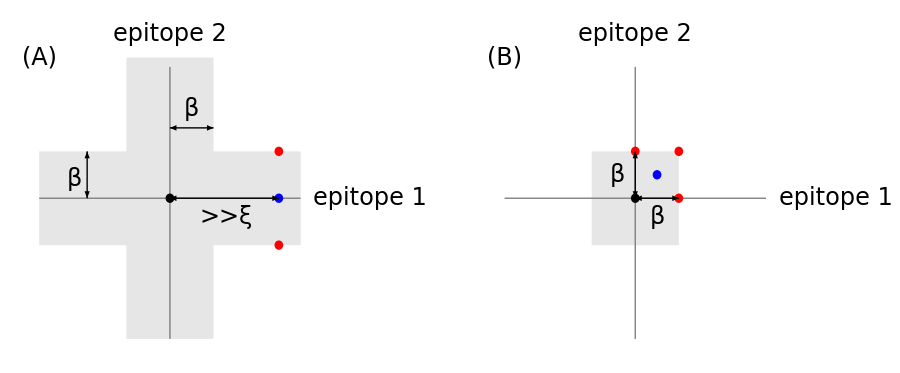

```mathematica
strainatorigin2 = Graphics[Disk[{0,0},.1]];
xaxis = Graphics[{Gray,Line[{{-3,0},{3,0}}]}];
yaxis = Graphics[{Gray,Line[{{0,2.8},{0,-3}}]}];
xaxislabel = Graphics[Text[Style["epitope 1",FontSize->24],{4.6,0}]];
yaxislabel = Graphics[Text[Style["epitope 2",FontSize->24], {0,3.5}]];
allaxes = Show[xaxis,yaxis,xaxislabel,yaxislabel];
everynbdgap1 = Graphics[{GrayLevel[0.9],Rectangle[{1,-3},{-1,3}(*{-3,1},{3,-1}*)]}];
everynbdgap2 = Graphics[{GrayLevel[0.9],Rectangle[{-3,1},{3,-1}]}];
everygappoint = Graphics[{Blue,Disk[{2.5,0},.1]}];(*Triangle[{{2.25,-.2},{2.75,-.2},{2.5,.3}}]}];*)
closeststrain1every = Graphics[{Red,Disk[{2.5,1},.1]}];
closeststrain2every = Graphics[{Red,Disk[{2.5,-1},.1]}];
everygapplot=Show[everynbdgap1, everynbdgap2,allaxes,everygappoint, strainatorigin2, closeststrain1every,closeststrain2every,
Graphics[Text[Style["β",FontSize->24],{-2.2,0.4}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{-1.9,1},{-1.9,0}}]}],
Graphics[Text[Style["β",FontSize->24],{.5,1.9}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{0,1.5},{1,1.5}}]}],
Graphics[Text[Style["(A)",FontSize->24],{-3,3}]],
Graphics[Text[Style[">>ξ",FontSize->24],{1.3,-0.4}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{0,0},{2.5,0}}]}],
ImageSize->300];

anynbdgap = Graphics[{GrayLevel[0.9],Rectangle[{-1,1},{1,-1}]}];
anygappoint = Graphics[{Blue,Disk[{.5,.5},0.1]}];(*Triangle[{{.25,.25},{.75,.25},{.5,.75}}]}];*)
closeststrain1any = Graphics[{Red,Disk[{0,1},.1]}];
closeststrain2any = Graphics[{Red,Disk[{1,0},.1]}];
closeststrain3any = Graphics[{Red,Disk[{1,1},.1]}];
strainatoriginany = Graphics[{Black,Disk[{0,0},.1]}];
anygapplot=Show[anynbdgap,allaxes,anygappoint,strainatoriginany, closeststrain1any, closeststrain2any,closeststrain3any,
Graphics[Text[Style["β",FontSize->24],{-0.4,0.5}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{0,1},{0,0}}]}],
Graphics[Text[Style["β",FontSize->24],{0.5,-0.4}]],
Graphics[{Arrowheads[{-.02,.02}],Arrow[{{0,0},{1,0}}]}],
Graphics[Text[Style["(B)",FontSize->24],{-3,3}]],
ImageSize->300];
bothgapplots =
GraphicsRow[{everygapplot,anygapplot,PointLegend[{Black,Red,Blue, GrayLevel[0.9]},{"strain in mem","allowed strain","immunity gap strain","excluded region"},LegendMarkers->{Graphics[{Disk[{0,0},5]}],Graphics[{Disk[{0,0},5]}],Graphics[{Disk[{0,0},5]}], Graphics[{Rectangle[{-.1,-.1},{.1,.1}]}]},
LegendMarkerSize->15,LabelStyle->{FontSize->24}]}, ImageSize->900]
```